## Initialization commands

```mathematica
SetDirectory[NotebookDirectory[]];
```

### Basic data import & manipulation

```mathematica
datapath=FileNameJoin[{"surveydata","classical"}]; (* path to optimization files *)

(* Import NPY array as List *)
ImportNPY[file_]:=Module[{a,f=OpenRead[file,BinaryFormat->True],version,headerlen,header,dims,type,typ,byto},a=If[BinaryRead[f,"Byte"]==147&&BinaryReadList[f,"Character8",5]==Characters["NUMPY"],version=BinaryReadList[f,"Byte",2];
headerlen=BinaryRead[f,"Integer16",ByteOrdering->-1];
header=StringJoin@BinaryReadList[f,"Character8",headerlen];
dims=StringCases[header,"'shape':"~~Whitespace~~"("~~s:{NumberString,",",Whitespace}..~~")":>ToExpression["{"~~If[StringTake[s,-1]==",",StringDrop[s,-1],s]~~"}"]][[1]];
type=StringCases[header,"'descr':"~~Whitespace~~Shortest["'"~~s:_...~~"'"]:>s][[1]];
byto=Switch[StringTake[type,1],"<",-1,">",1,_,$ByteOrdering];
If[MemberQ[{"<",">","|","="},StringTake[type,1]],type=StringDrop[type,1]];
typ=Switch[type,"f8","Real64","i8","Integer64",_,Print["unknown type",header];0];
If[typ≠0,ArrayReshape[BinaryReadList[f,typ,ByteOrdering->byto],dims],0],Print["not a npy"];0];
Close[f];a];

(* Import NPY model tensor for a given sequence seq with dimension d and s symbols;
Returns a s×d×d tensor T as a list, so that T0 = T[[1]];
Usually, it's best to canonize the order of states too with, e.g.: CanonicalOrder[ImportTModel[seq, d],seq];
Sequence is a list of symbols, e.g.: {0,0,1,0,1,1}
 *)
ImportTModel[seq0_,d_:2,s_:2]:=Quiet@Module[{t,i,l,fn,seq},l=Length[seq0];
seq=If[seq0[[1]]==1,1-seq0,seq0];
fn=FileNameJoin[{NotebookDirectory[],datapath,"T_S"<>ToString[s]<>"_L"<>StringPadLeft[ToString[l],2,"0"]<>"_D"<>StringPadLeft[ToString[Max[1,d]],2,"0"]<>"_"<>Map[ToString,seq]<>".npy"}];If[FileExistsQ[fn],t=ImportNPY[fn];For[i=1,i≤d,i++,t[[All,i,All]]/=Total@Flatten[t[[All,i,All]]]];t,
Print["No data for "<>FileBaseName[fn]<>".npy"];Abort[];
]];

(* Given a model and a sequence, compute total probability. *)
ComputeProbability[t_,seq_,trunc_:-1,initial_:1]:=Module[{d,vpi,veta},
d=Dimensions[t][[2]];
vpi={Map[KroneckerDelta,Range[1,d]-initial]};
veta=ConstantArray[1,{d,1}];
Det[vpi.(Dot@@(
Join@@{
{IdentityMatrix[Dimensions[t][[2]]]},
t[[#+1]]&/@Take[seq,If[trunc<0,Length[seq],trunc]]
}
)).veta]
];
(* Same as above, but don't multiply by eta *)
ComputeProbabilityVector[t_,seq_,trunc_:-1,initial_:1]:=Module[{d,vpi,veta},
d=Dimensions[t][[2]];
vpi={Map[KroneckerDelta,Range[1,d]-initial]};
veta=ConstantArray[1,{Dimensions[t][[2]],1}];
Flatten[vpi.(Dot@@(
Join@@{
{IdentityMatrix[Dimensions[t][[2]]]},
t[[#+1]]&/@Take[seq,Clip[If[trunc<0,Length[seq],trunc],{0,Length[seq]}]]
}
))]
];
```

### Useful functions

```mathematica
(* Clock sequence of length L. This is the term we used before we settled on "one-tick sequence". *)
OneTickSequence[L_]:=Map[KroneckerDelta,Range[1,L]-L];
ClockSequence[L_]:=OneTickSequence[L];

(* Exact computation based on the (deterministic steps)+(cycle) analysis *)
(* We assume a length ldet=0..L for the deterministic part and 1..(L-ldet for the cycle *)
(* Whenever we find a better bound dc, we collect all patterns (ldet,lcy) where ldet+lcy=dc *)
(* We stop once ldet > dc, since we can only do worse after that. *)
DCPatterns[seq_]:=Module[{ldet,lcy,L,dc,patts,s},
L=Length[seq];dc=L;patts={};
For[ldet=0,ldet≤dc,ldet++,For[lcy=1,lcy≤Length[seq]-ldet,lcy++,
s=Take[Flatten[{
Take[seq,ldet],
ConstantArray[Take[Drop[seq,ldet],lcy],Ceiling[(L-ldet)/lcy]]
}],L];
If[seq==s&&(ldet+lcy)≤dc,
If[(ldet+lcy)<dc,dc=ldet+lcy;patts={};];AppendTo[patts,{ldet,lcy}];
];
]];
{dc,patts}
];
(* Returns the string version of the patterns: 00(10) etc. *)
(* aligned=True adds spaces between symbols so the symbols align nicely *)
Clear[DCPatternStrings]
DCPatternStrings[seq_,aligned_:False]:=Module[{pats,p,ps,dc},
{dc,pats}=DCPatterns[seq];
If[aligned,
Table[
ps=Flatten@Join[Thread[{ConstantArray[" ",dc],Map[ToString,Take[seq,dc]]}]];
ps[[2p[[1]]+1]]="(";ps<>")",
{p,pats}
],
Table[
Take[Map[ToString,seq],p[[1]]]<>"("<>Take[Drop[Map[ToString,seq],p[[1]]],p[[2]]]<>")",
{p,pats}
]
]
];
DC[seq_]:=DCPatterns[seq][[1]];

(* Given a sequence, a pattern specification {Subscript[L, ow],Subscript[L, cy]} and a target length L,
generates the extension of the pattern truncated to that length *)
ExtendPattern[seq_,pat_,L_]:=Take[Flatten[{Take[seq,pat[[1]]],ConstantArray[Take[Drop[seq,pat[[1]]],pat[[2]]],Ceiling[(L-pat[[1]])/pat[[2]]]]}],L];

(* Generates all the equivalent deterministic models for a given sequence *)
DCModels[seq_]:= Module[{pats,d,m,p,pseq,pcy,i},
{d,pats}=DCPatterns[seq];
Table[
m=ConstantArray[0,{2,d,d}];
For[i=1,i≤d-1,i++,
m[[seq[[i]]+1,i,i+1]]=1;
];
m[[seq[[d]]+1,d,d-p[[2]]+1]]=1;
m,
{p,pats}
]
];

(* Number of integer compositions, human-readable to avoid magic numbers *)
NIntegerCompositions[n_]:=2^(n-1);
GetIntegerComposition[n_,i_]:=Differences[Join[{0},Flatten@Position[IntegerDigits[i,2,n-1],1],{n}]];

Clear[GeneralizedMulticyclicModel]
(* Generates a symbolic GMCM *)
(* sig is the block sizes, e.g.: {3,2,1}, giving d = 3+2+1 = 6 states *)
(* final is which state the final "1" transition goes to, starting from 1. final=0 sets it to the last state. *)
GeneralizedMulticyclicModel[sig_,var_,final_:0]:=Module[{m,b,i},
m=DiagonalMatrix[Range[1,Length[sig]]];
If[Length[sig]>1,m+=100DiagonalMatrix[Range[1,Length[sig]-1],1]];
m=m/.(
(b=If[
#[[2]]>1,
 DiagonalMatrix[ConstantArray[1,#[[2]]-1],1]
,
var[#[[1]]]
];
If[#[[2]]>1,b[[#[[2]],#[[2]]]]=0;b[[#[[2]],1]]=var[#[[1]]]];
#[[1]]->b)&/@Thread[{Range[1,Length[sig]],sig}]
);
For[i=1,i<Length[sig],i++,
b=ConstantArray[0,{sig[[i]],sig[[i+1]]}];
b[[sig[[i]],1]]=1-var[i];
m=m/.{100i->b};
];
b=ConstantArray[0,Total[sig]{1,1}];
b[[Total[sig],If[final==0,Total[sig],final]]]=1-var[Length[sig]];
{ArrayFlatten[m],b}
];
(* Visualizes a GMCM in block-matrix form *)
BlockMatrixForm[m_,sig_]:=Module[{div},
div=Map[If[#==1,True,False]&,Total[Map[KroneckerDelta,Range[0,Total[sig]-1]-#]&/@Accumulate[sig]]];
MatrixForm[{{Grid[m,Dividers->{div,div},ItemSize->Full]}}]
];
```

### Canonization

```mathematica
(* Rearranges the states in a model into a canonical form. See section 1 for the description. *)
(* Requires the model and its sequence it optimizes *)
CanonicalOrder[t0_,seq_,initial_:1]:=Module[{d,ev,i,o,p},
d=Dimensions[t0][[2]];
ev=Round[ComputeProbabilityVector[t0,seq,#,initial]&/@Range[0,Length[seq]],10.0^-6]; (* sequence of probability vectors for 0-L steps *)
o=Position[ev[[All,#]],_?(#>0&),1,1]&/@Range[1,d]; (* position of the first non-zero step for each state *)
o=If[Length[#]==0,Length[seq],#[[1,1]]]&/@o;
o=GroupBy[Thread[{#,o[[#]],ev[[o[[#]],#]]}]&/@Range[1,d],#[[2]]&]; (* group states by first non-zero position *)
o=ArrayFlatten[Table[Sort[o[i],#1[[3]]>#2[[3]]&],{i,Sort@Keys[o]}],1][[All,1]]; (* sort states within groups by decreasing probability and get final order *)
p=IdentityMatrix[d][[o]]; (* construct the permutation matrix that reorders states *)
(p.#.Transpose[p]&)/@t0 (* apply the permutation for T0 and T1 and return the reodered state *)
];
(*If[DEBUG,
seq={0,0,0,0,0,1};d=Length[seq]-1;
t=ImportTModel[seq,d];
Print[{MatrixForm/@Round[t,0.001],ViewModelGraph[t,seq,True]}];
t=CanonicalOrder[t,seq];
Print[{MatrixForm/@Round[t,0.001],ViewModelGraph[t,seq,True]}];
]*)
```

### Visualization

```mathematica
(* Typical ArrayPlot, but fixing 0=white 1=black, without automatic normalization of dataset *)
NormalizedArrayPlot[data_,opts___]:=ArrayPlot[data,ColorFunctionScaling->False,ColorFunction->(Hue[0,0,1-#]&),opts]

(* Visualizes the sequence as a row of black/white squares *)
(* The optional parameter k places a red line after the k-th square *)
ViewSequence[seq_,k_:0]:=ArrayPlot[{seq},ColorRules->{0->Hue[0,0,0.9],1->Black},Mesh->All,
Epilog->If[k≠0,{Red,AbsoluteThickness[2],Line[{{k,0},{k,1}}]},{}],
ImageSize->100,Frame->None];

(* Visualize model tensor using squares instead of numbers. The parameter s specifies the size *)
ViewModelMatrix[m_,s_:40]:=Module[{t},Table[ArrayPlot[t,FrameTicks->None,ImageSize->s,PlotRangePadding->0,ColorFunctionScaling->False,ColorFunction->(Hue[0,0,1-#]&)],{t,m}]];
```

## Survey of generalized multicyclic models

For a fixed L, we optimize (using Mathematica, which may not be the best choice) over all possible
generalized multicyclic models of all possible d and initial states.

The optimal values are shown in a table.
The first column is the dimension d, which defines a block of all cycle decompositions.
Within each block, each decomposition is sorted in descending order of optimal probability found.

The 2nd column is the probability for a given signature, the 3rd column the signature e.g. (3,1,1), the
4th column the initial state (always within the first cycle), and then T0 and T1.

```mathematica
If[True,
fn=FileNameJoin[{NotebookDirectory[],"surveydata","gmcmdata.mx"}];
If[FileExistsQ[fn],
data=Import[fn],
data=<|Table[
L-> <|Table[
od=Table[
(*c=Sort[GetIntegerComposition[d,i]];*)
c=GetIntegerComposition[d,i];
m=GeneralizedMulticyclicModel[c,x];
is=Table[{s,NMaximize[Flatten@{
ComputeProbability[m,ClockSequence[L],-1,s],
0≤x[#]<1&/@Range[1,Length[c]]
},
x[#]&/@Range[1,Length[c]]
]},{s,1,c[[1]]}];
is=Sort[is,#1[[2,1]]>#2[[2,1]]&];
is=is[[1]];
t=m/.#[[2]]&@is[[2]];
p=#[[1]]&@is[[2]];
tview=(BlockMatrixForm[#,c]&/@Round[t,0.001])&@is[[2]];
<|{"sig"-> c,"p"->p,"T"->t,"is"->is[[1]]}|>
,
{i,0,2^(d-1)-1}
];
d->Select[od,Abs[#["p"]-Max[od[[All,"p"]]]]≤0.0001&],
{d,1,L-1}
]|>
,{L,1,10}
]|>;
Export[NotebookDirectory[]<>"surveydata\\gmcmdata.mx",data];
];
gmcmdata=data;
]
```

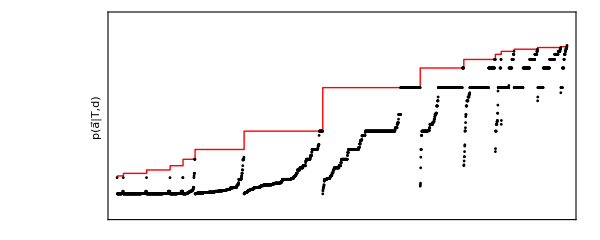

```mathematica
sp=0.001;(* sorting precision *)
L=10;
plt=ListPlot[
(Transpose@SortBy[
ArrayFlatten[Table[
Table[
Round[{
ComputeProbability[ImportTModel[seq,dseq],seq],
Mean@data[DC[seq]][dseq][[All,"p"]],
DC[seq],
dseq
},sp],
{dseq,1,DC[seq]-1}
],
{seq,IntegerDigits[#,2,L]&/@Range[1,2^(L-1)-1]}
],1],
{#[[2]]&,#[[1]]&,#[[1]]0&,#[[1]]0&}
])[[{1,2},All]],
Joined->{False,True,True,True},InterpolationOrder->0,
PlotStyle->{
{AbsoluteThickness[1],AbsolutePointSize[2],Black},
{AbsoluteThickness[1],Red}
},
ImageSize->600,Frame->True,AspectRatio->0.4,FrameTicks->{{None,{{0.0,"0.0"},0.1,0.2,0.3,{1.0/E,"1/ⅇ"}}},{None,None}},
FrameStyle->AbsoluteThickness[1.25],
PlotRange->{All,{-0.05,1/E+0.05}},LabelStyle->{FontFamily->"Calibri",FontColor->Black,FontSize->17},
GridLines->{None,{0,{1/E,Blue}}},FrameLabel->{{"p(a⃗|T,d)",None},{None,None}}
]
Export[FileNameJoin[{NotebookDirectory[],"conjecture_L10_G_p.pdf"}],plt]
```

## GMCM vs signatures

```mathematica
sig={1,3,3};
L=13;

d=Total[sig];
{L,d}
sig
SortBy[Table[
Append[NMaximize[{
ComputeProbability[GeneralizedMulticyclicModel[sig,q],ClockSequence[L],-1,i],
(0≤#≤1&)/@Array[q,Length[sig]]},
Array[q,Length[sig]]],i],
{i,1,sig[[1]]}
],-#[[1]]&]//TableForm
sig2=ConstantArray[Floor[Total[sig]/Length[sig]],Length[sig]];
δ=Total[sig]-Total[sig2];
{δ,sig2}
SortBy[Table[
Append[NMaximize[{
ComputeProbability[GeneralizedMulticyclicModel[sig2,q],ClockSequence[L-δ],-1,i],
(0≤#≤1&)/@Array[q,Length[sig2]]},
Array[q,Length[sig2]]],i],
{i,1,sig2[[1]]}
],-#[[1]]&]//TableForm
```

```mathematica
fn=NotebookDirectory[]<>"emcmdata.mx";
Dynamic[Keys[emcmdata]]
If[FileExistsQ[fn],
emcmdata=Import[fn],
emcmdata=Association[];
Module[{L0,d0,n0,k0,t0,z0,is,sig,m,opt},Do[
Clear[n,k,t,z];
emcmdata[{L0,d0}]=First@SortBy[Table[
n0=Floor[d0/k0];
t0=d0-n0 k0;
sig=DeleteCases[Join[ConstantArray[k0,n0],{t0}],0];
m=GeneralizedMulticyclicModel[sig,q];
If[t0≠0,m=m/.(q[Length[sig]]->0)];
m=m/.(#->q&/@Array[q,Length[sig]]);
(*Print[{sig,MatrixForm/@m}];*)
opt=SortBy[Table[
Join[NMaximize[{
ComputeProbability[m,ClockSequence[L0],-1,is],
0≤q≤1
},q],{is}],
{is,1,k0}
],-#[[1]]&];
opt=First[opt];
z0=opt[[3]];
{{n->n0,k->k0,t->t0,z->z0},opt[[1]],opt[[2,1,2]]},
{k0,1,d0}
],-#[[2]]&];
Export[fn,emcmdata];
,
{L0,2,32},
{d0,1,L0-1}
]];
];
emcmdata
```

```mathematica
TableForm[Table[
"("<>StringRiffle[Map[ToString,({n,k,t,z-1}/.#[[1]]&)@emcmdata[{L,d}]],","]<>")",
{L,2,20},{d,1,L-1}
]]
```

(1,1,0,0) |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
(1,1,0,0) | (2,1,0,0) |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
(1,1,0,0) | (1,2,0,0) | (3,1,0,0) |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
(1,1,0,0) | (1,2,0,1) | (1,2,1,0) | (4,1,0,0) |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
(1,1,0,0) | (1,2,0,0) | (1,3,0,0) | (2,2,0,0) | (5,1,0,0) |  |  |  |  |  |  |  |  |  |  |  |  |  | 
(1,1,0,0) | (1,2,0,1) | (1,2,1,0) | (1,3,1,0) | (2,2,1,0) | (6,1,0,0) |  |  |  |  |  |  |  |  |  |  |  |  | 
(1,1,0,0) | (1,2,0,0) | (1,3,0,1) | (1,4,0,0) | (1,3,2,0) | (3,2,0,0) | (7,1,0,0) |  |  |  |  |  |  |  |  |  |  |  | 
(1,1,0,0) | (1,2,0,1) | (1,3,0,0) | (1,3,1,1) | (1,4,1,0) | (2,3,0,0) | (3,2,1,0) | (8,1,0,0) |  |  |  |  |  |  |  |  |  |  | 
(1,1,0,0) | (1,2,0,0) | (1,3,0,2) | (1,3,1,0) | (1,5,0,0) | (1,4,2,0) | (2,3,1,0) | (4,2,0,0) | (9,1,0,0) |  |  |  |  |  |  |  |  |  | 
(1,1,0,0) | (1,2,0,1) | (1,3,0,1) | (1,4,0,1) | (1,3,2,0) | (1,5,1,0) | (1,4,3,0) | (2,3,2,0) | (4,2,1,0) | (10,1,0,0) |  |  |  |  |  |  |  |  | 
(1,1,0,0) | (1,2,0,0) | (1,3,0,0) | (1,4,0,0) | (1,4,1,1) | (1,6,0,0) | (1,5,2,0) | (2,4,0,0) | (3,3,0,0) | (5,2,0,0) | (11,1,0,0) |  |  |  |  |  |  |  | 
(1,1,0,0) | (1,2,0,1) | (1,3,0,2) | (1,3,1,0) | (1,4,1,0) | (1,4,2,1) | (1,6,1,0) | (1,5,3,0) | (2,4,1,0) | (3,3,1,0) | (5,2,1,0) | (12,1,0,0) |  |  |  |  |  |  | 
(1,1,0,0) | (1,2,0,0) | (1,3,0,1) | (1,4,0,2) | (1,5,0,1) | (1,4,2,0) | (1,7,0,0) | (1,6,2,0) | (1,5,4,0) | (2,4,2,0) | (3,3,2,0) | (6,2,0,0) | (13,1,0,0) |  |  |  |  |  | 
(1,1,0,0) | (1,2,0,1) | (1,3,0,0) | (1,4,0,1) | (1,5,0,0) | (1,5,1,1) | (1,4,3,0) | (1,7,1,0) | (1,6,3,0) | (2,5,0,0) | (2,4,3,0) | (4,3,0,0) | (6,2,1,0) | (14,1,0,0) |  |  |  |  | 
(1,1,0,0) | (1,2,0,0) | (1,3,0,2) | (1,4,0,0) | (1,4,1,1) | (1,5,1,0) | (1,5,2,1) | (1,8,0,0) | (1,7,2,0) | (1,6,4,0) | (2,5,1,0) | (3,4,0,0) | (4,3,1,0) | (7,2,0,0) | (15,1,0,0) |  |  |  | 
(1,1,0,0) | (1,2,0,1) | (1,3,0,1) | (1,4,0,3) | (1,4,1,0) | (1,6,0,1) | (1,5,2,0) | (1,5,3,1) | (1,8,1,0) | (1,7,3,0) | (1,6,5,0) | (2,5,2,0) | (3,4,1,0) | (4,3,2,0) | (7,2,1,0) | (16,1,0,0) |  |  | 
(1,1,0,0) | (1,2,0,0) | (1,3,0,0) | (1,4,0,2) | (1,5,0,2) | (1,6,0,0) | (1,6,1,1) | (1,5,3,0) | (1,9,0,0) | (1,8,2,0) | (1,7,4,0) | (2,6,0,0) | (2,5,3,0) | (3,4,2,0) | (5,3,0,0) | (8,2,0,0) | (17,1,0,0) |  | 
(1,1,0,0) | (1,2,0,1) | (1,3,0,2) | (1,4,0,1) | (1,5,0,1) | (1,5,1,2) | (1,6,1,0) | (1,6,2,1) | (1,5,4,0) | (1,9,1,0) | (1,8,3,0) | (1,7,5,0) | (2,6,1,0) | (2,5,4,0) | (3,4,3,0) | (5,3,1,0) | (8,2,1,0) | (18,1,0,0) | 
(1,1,0,0) | (1,2,0,0) | (1,3,0,1) | (1,4,0,0) | (1,5,0,0) | (1,5,1,1) | (1,7,0,1) | (1,6,2,0) | (1,6,3,1) | (1,10,0,0) | (1,9,2,0) | (1,8,4,0) | (1,7,6,0) | (2,6,2,0) | (3,5,0,0) | (4,4,0,0) | (5,3,2,0) | (9,2,0,0) | (19,1,0,0)

```mathematica
fn=NotebookDirectory[]<>"emcmdatafull.mx";
Dynamic[Keys[emcmdata]]
If[FileExistsQ[fn],
emcmdata=Import[fn],
emcmdata=Association[];
Module[{L0,d0,n0,k0,t0,z0,is,sig,m,opt},Do[
Clear[n,k,t,z];
emcmdata[{L0,d0}]=SortBy[Table[
n0=Floor[d0/k0];
t0=d0-n0 k0;
sig=DeleteCases[Join[ConstantArray[k0,n0],{t0}],0];
m=GeneralizedMulticyclicModel[sig,q];
If[t0≠0,m=m/.(q[Length[sig]]->0)];
m=m/.(#->q&/@Array[q,Length[sig]]);
(*Print[{sig,MatrixForm/@m}];*)
opt=SortBy[Table[
Join[NMaximize[{
ComputeProbability[m,ClockSequence[L0],-1,is],
0≤q≤1
},q],{is}],
{is,1,k0}
],-#[[1]]&];
opt=First[opt];
z0=opt[[3]];
{{n->n0,k->k0,t->t0,z->z0},opt[[1]],opt[[2,1,2]]},
{k0,1,d0}
],-#[[2]]&];
Export[fn,emcmdata];
,
{L0,2,32},
{d0,1,L0-1}
]];
];
```

```mathematica
If[True,
Clear[ViewSequenceLabels];
ViewSequenceLabels[seq_,size_:Automatic]:=Module[{i},
Graphics[Table[
{
If[seq[[i]]==1,Hue[0,0,0.3],Hue[0,0,0.95]],
EdgeForm[Directive[Black,AbsoluteThickness[1]]],
Rectangle[{i-1,0},{i,1}],
{If[seq[[i]]==0,Black,White],
Text[Style[ToString[seq[[i]]],FontFamily->"Cambria",FontSize->0.75size],{i-0.5,0.48}]}
},
{i,1,Length[seq]}
],
ImageSize->{Automatic,size}
]
];

plt=Table[
k=1;
tbl=Table[
d=DC[seq]-k;
tc=CanonicalOrder[ImportTModel[seq,d],seq];
p=If[seq==ClockSequence[Length[seq]],
emcmdata[{Length[seq],d}][[2]],
ComputeProbability[tc,seq]
];
If[seq==ClockSequence[Length[seq]],
sig=DeleteCases[Join[ConstantArray[#[[1,2,2]],#[[1,1,2]]],{#[[1,3,2]]}],0]&@emcmdata[{L,d}];
tc=(GeneralizedMulticyclicModel[sig,q]&)@emcmdata[{L,d}];
tc=tc/.(#->emcmdata[{L,d}][[3]]&/@Array[q,Length[sig]]);
];
{
DC[seq],
DC[seq]-k,
Style[StringRiffle[Map[ToString,seq],""],FontFamily->"Cambria",FontSize->14],
ViewSequenceLabels[seq,20],
p,
ToString@DecimalForm[p,{6,6}],
TableForm[{ViewModelMatrix[tc]},TableSpacing->{0,0.5}]
},
{seq,IntegerDigits[Range[1,2^(L-1)-1],2,L]}
];
tbl=SortBy[tbl,{-#[[1]]&,-#[[5]]&}];
tbl=Join[{Style[#,FontWeight->Bold]&/@{"DC","d","Sequence","Sequence","p","p","Model"}},tbl];
ml=Join[{""},tbl[[All,1]],{""}];

Grid[
tbl[[All,{1,2,3,6,7}]],
Dividers->{All,
DeleteCases[Table[
ml[[i]]≠ml[[i+1]],
{i,1,Length[ml]-1}
],0]
},
Spacings->{2,1},
Alignment->{Center,Center}, 
Background->{Automatic,{Hue[0,0,0.95]}}
],
{L,3,6}
];
plt
(*Export[
NotebookDirectory[]<>"comparisons.svg",
TableForm[
{plt},
TableAlignments->{Left,Top}
]
]*)
]
```

{DC | d | Sequence | p | Model
3 | 2 | 001 | 0.296296 | -Graphics- | -Graphics-
2 | 1 | 010 | 0.148148 | -Graphics- | -Graphics-
2 | 1 | 011 | 0.148148 | -Graphics- | -Graphics-,DC | d | Sequence | p | Model
4 | 3 | 0001 | 0.316406 | -Graphics- | -Graphics-
3 | 2 | 0010 | 0.296296 | -Graphics- | -Graphics-
3 | 2 | 0100 | 0.250000 | -Graphics- | -Graphics-
3 | 2 | 0011 | 0.250000 | -Graphics- | -Graphics-
3 | 2 | 0110 | 0.250000 | -Graphics- | -Graphics-
2 | 1 | 0111 | 0.105469 | -Graphics- | -Graphics-
2 | 1 | 0101 | 0.062500 | -Graphics- | -Graphics-,DC | d | Sequence | p | Model
5 | 4 | 00001 | 0.327680 | -Graphics- | -Graphics-
4 | 3 | 00010 | 0.316406 | -Graphics- | -Graphics-
4 | 3 | 01100 | 0.296296 | -Graphics- | -Graphics-
4 | 3 | 01110 | 0.296296 | -Graphics- | -Graphics-
4 | 3 | 01011 | 0.296296 | -Graphics- | -Graphics-
4 | 3 | 00110 | 0.296296 | -Graphics- | -Graphics-
4 | 3 | 00011 | 0.296296 | -Graphics- | -Graphics-
3 | 2 | 01000 | 0.250000 | -Graphics- | -Graphics-
3 | 2 | 01101 | 0.250000 | -Graphics- | -Graphics-
3 | 2 | 00111 | 0.250000 | -Graphics- | -Graphics-
3 | 2 | 00100 | 0.190044 | -Graphics- | -Graphics-
3 | 2 | 00101 | 0.163840 | -Graphics- | -Graphics-
3 | 2 | 01001 | 0.163840 | -Graphics- | -Graphics-
2 | 1 | 01111 | 0.081920 | -Graphics- | -Graphics-
2 | 1 | 01010 | 0.034560 | -Graphics- | -Graphics-,DC | d | Sequence | p | Model
6 | 5 | 000001 | 0.334898 | -Graphics- | -Graphics-
5 | 4 | 000010 | 0.327680 | -Graphics- | -Graphics-
5 | 4 | 011110 | 0.316406 | -Graphics- | -Graphics-
5 | 4 | 000011 | 0.316406 | -Graphics- | -Graphics-
5 | 4 | 000110 | 0.316406 | -Graphics- | -Graphics-
5 | 4 | 011100 | 0.316406 | -Graphics- | -Graphics-
5 | 4 | 001110 | 0.296296 | -Graphics- | -Graphics-
5 | 4 | 010100 | 0.296296 | -Graphics- | -Graphics-
5 | 4 | 001011 | 0.296296 | -Graphics- | -Graphics-
5 | 4 | 010011 | 0.250000 | -Graphics- | -Graphics-
4 | 3 | 000100 | 0.316406 | -Graphics- | -Graphics-
4 | 3 | 011101 | 0.296296 | -Graphics- | -Graphics-
4 | 3 | 011001 | 0.296296 | -Graphics- | -Graphics-
4 | 3 | 001000 | 0.296296 | -Graphics- | -Graphics-
4 | 3 | 000111 | 0.296296 | -Graphics- | -Graphics-
4 | 3 | 010110 | 0.250000 | -Graphics- | -Graphics-
4 | 3 | 011010 | 0.250000 | -Graphics- | -Graphics-
4 | 3 | 011000 | 0.250000 | -Graphics- | -Graphics-
4 | 3 | 000101 | 0.250000 | -Graphics- | -Graphics-
4 | 3 | 010001 | 0.250000 | -Graphics- | -Graphics-
4 | 3 | 010111 | 0.250000 | -Graphics- | -Graphics-
4 | 3 | 001100 | 0.250000 | -Graphics- | -Graphics-
4 | 3 | 001101 | 0.250000 | -Graphics- | -Graphics-
3 | 2 | 001111 | 0.250000 | -Graphics- | -Graphics-
3 | 2 | 010000 | 0.250000 | -Graphics- | -Graphics-
3 | 2 | 010010 | 0.163840 | -Graphics- | -Graphics-
3 | 2 | 001010 | 0.163840 | -Graphics- | -Graphics-
3 | 2 | 011011 | 0.148148 | -Graphics- | -Graphics-
3 | 2 | 001001 | 0.087791 | -Graphics- | -Graphics-
2 | 1 | 011111 | 0.066980 | -Graphics- | -Graphics-
2 | 1 | 010101 | 0.015625 | -Graphics- | -Graphics-}

```mathematica
Do[
ms=(#[Max[Keys[#]]]&)@GroupBy[emcmdata[{L,d}],Round[#[[2]],0.000001]&];
If[Length[ms]>1,
Print[{L,d}];
Print[TableForm[{ms}]];
]
,
{L,2,10},{d,1,L-1}
]
```

{5,3}

n→1 | 1→2 | {{{2.30169×10^-9,6.64986×10^-18,1.06434×10^-19,1.,1.12549×10^-12},{5.38564×10^-13,5.14158×10^-12,1.,3.64555×10^-22,2.33807×10^-15},{5.08458×10^-22,3.70084×10^-18,2.42281×10^-10,1.22645×10^-20,2.36062×10^-20},{1.53092×10^-21,9.13356×10^-17,2.87131×10^-15,1.82981×10^-9,1.},{1.68238×10^-23,1.,3.09312×10^-11,1.54826×10^-21,2.84246×10^-10}},{{2.7136×10^-18,4.00992×10^-25,5.67351×10^-24,1.76755×10^-24,3.13352×10^-20},{2.88201×10^-11,1.53354×10^-15,1.63451×10^-24,4.53239×10^-8,9.80152×10^-10},{0.388766,8.18448×10^-20,5.17968×10^-22,0.310998,0.300237},{6.50519×10^-25,2.8742×10^-22,2.85115×10^-22,9.71925×10^-24,3.50925×10^-21},{7.33398×10^-21,8.83195×10^-20,5.45289×10^-24,3.86524×10^-21,3.55669×10^-25}}}→1 | z→1
0.25 |  |  | 
0.5 |  |  |  | n→1 | 1→3 | {{{2.30169×10^-9,6.64986×10^-18,1.06434×10^-19,1.,1.12549×10^-12},{5.38564×10^-13,5.14158×10^-12,1.,3.64555×10^-22,2.33807×10^-15},{5.08458×10^-22,3.70084×10^-18,2.42281×10^-10,1.22645×10^-20,2.36062×10^-20},{1.53092×10^-21,9.13356×10^-17,2.87131×10^-15,1.82981×10^-9,1.},{1.68238×10^-23,1.,3.09312×10^-11,1.54826×10^-21,2.84246×10^-10}},{{2.7136×10^-18,4.00992×10^-25,5.67351×10^-24,1.76755×10^-24,3.13352×10^-20},{2.88201×10^-11,1.53354×10^-15,1.63451×10^-24,4.53239×10^-8,9.80152×10^-10},{0.388766,8.18448×10^-20,5.17968×10^-22,0.310998,0.300237},{6.50519×10^-25,2.8742×10^-22,2.85115×10^-22,9.71925×10^-24,3.50925×10^-21},{7.33398×10^-21,8.83195×10^-20,5.45289×10^-24,3.86524×10^-21,3.55669×10^-25}}}→0 | z→2
0.25 |  |  | 
0.5 |  |  |

{7,3}

n→1 | 1→2 | {{{2.30169×10^-9,6.64986×10^-18,1.06434×10^-19,1.,1.12549×10^-12},{5.38564×10^-13,5.14158×10^-12,1.,3.64555×10^-22,2.33807×10^-15},{5.08458×10^-22,3.70084×10^-18,2.42281×10^-10,1.22645×10^-20,2.36062×10^-20},{1.53092×10^-21,9.13356×10^-17,2.87131×10^-15,1.82981×10^-9,1.},{1.68238×10^-23,1.,3.09312×10^-11,1.54826×10^-21,2.84246×10^-10}},{{2.7136×10^-18,4.00992×10^-25,5.67351×10^-24,1.76755×10^-24,3.13352×10^-20},{2.88201×10^-11,1.53354×10^-15,1.63451×10^-24,4.53239×10^-8,9.80152×10^-10},{0.388766,8.18448×10^-20,5.17968×10^-22,0.310998,0.300237},{6.50519×10^-25,2.8742×10^-22,2.85115×10^-22,9.71925×10^-24,3.50925×10^-21},{7.33398×10^-21,8.83195×10^-20,5.45289×10^-24,3.86524×10^-21,3.55669×10^-25}}}→1 | z→1
0.148148 |  |  | 
0.666667 |  |  |  | n→1 | 1→3 | {{{2.30169×10^-9,6.64986×10^-18,1.06434×10^-19,1.,1.12549×10^-12},{5.38564×10^-13,5.14158×10^-12,1.,3.64555×10^-22,2.33807×10^-15},{5.08458×10^-22,3.70084×10^-18,2.42281×10^-10,1.22645×10^-20,2.36062×10^-20},{1.53092×10^-21,9.13356×10^-17,2.87131×10^-15,1.82981×10^-9,1.},{1.68238×10^-23,1.,3.09312×10^-11,1.54826×10^-21,2.84246×10^-10}},{{2.7136×10^-18,4.00992×10^-25,5.67351×10^-24,1.76755×10^-24,3.13352×10^-20},{2.88201×10^-11,1.53354×10^-15,1.63451×10^-24,4.53239×10^-8,9.80152×10^-10},{0.388766,8.18448×10^-20,5.17968×10^-22,0.310998,0.300237},{6.50519×10^-25,2.8742×10^-22,2.85115×10^-22,9.71925×10^-24,3.50925×10^-21},{7.33398×10^-21,8.83195×10^-20,5.45289×10^-24,3.86524×10^-21,3.55669×10^-25}}}→0 | z→3
0.148148 |  |  | 
0.666667 |  |  |

{7,4}

n→1 | 1→3 | {{{2.30169×10^-9,6.64986×10^-18,1.06434×10^-19,1.,1.12549×10^-12},{5.38564×10^-13,5.14158×10^-12,1.,3.64555×10^-22,2.33807×10^-15},{5.08458×10^-22,3.70084×10^-18,2.42281×10^-10,1.22645×10^-20,2.36062×10^-20},{1.53092×10^-21,9.13356×10^-17,2.87131×10^-15,1.82981×10^-9,1.},{1.68238×10^-23,1.,3.09312×10^-11,1.54826×10^-21,2.84246×10^-10}},{{2.7136×10^-18,4.00992×10^-25,5.67351×10^-24,1.76755×10^-24,3.13352×10^-20},{2.88201×10^-11,1.53354×10^-15,1.63451×10^-24,4.53239×10^-8,9.80152×10^-10},{0.388766,8.18448×10^-20,5.17968×10^-22,0.310998,0.300237},{6.50519×10^-25,2.8742×10^-22,2.85115×10^-22,9.71925×10^-24,3.50925×10^-21},{7.33398×10^-21,8.83195×10^-20,5.45289×10^-24,3.86524×10^-21,3.55669×10^-25}}}→1 | z→1
0.25 |  |  | 
0.5 |  |  |  | n→1 | 1→4 | {{{2.30169×10^-9,6.64986×10^-18,1.06434×10^-19,1.,1.12549×10^-12},{5.38564×10^-13,5.14158×10^-12,1.,3.64555×10^-22,2.33807×10^-15},{5.08458×10^-22,3.70084×10^-18,2.42281×10^-10,1.22645×10^-20,2.36062×10^-20},{1.53092×10^-21,9.13356×10^-17,2.87131×10^-15,1.82981×10^-9,1.},{1.68238×10^-23,1.,3.09312×10^-11,1.54826×10^-21,2.84246×10^-10}},{{2.7136×10^-18,4.00992×10^-25,5.67351×10^-24,1.76755×10^-24,3.13352×10^-20},{2.88201×10^-11,1.53354×10^-15,1.63451×10^-24,4.53239×10^-8,9.80152×10^-10},{0.388766,8.18448×10^-20,5.17968×10^-22,0.310998,0.300237},{6.50519×10^-25,2.8742×10^-22,2.85115×10^-22,9.71925×10^-24,3.50925×10^-21},{7.33398×10^-21,8.83195×10^-20,5.45289×10^-24,3.86524×10^-21,3.55669×10^-25}}}→0 | z→2
0.25 |  |  | 
0.5 |  |  |

{8,5}

n→1 | 1→3 | {{{2.30169×10^-9,6.64986×10^-18,1.06434×10^-19,1.,1.12549×10^-12},{5.38564×10^-13,5.14158×10^-12,1.,3.64555×10^-22,2.33807×10^-15},{5.08458×10^-22,3.70084×10^-18,2.42281×10^-10,1.22645×10^-20,2.36062×10^-20},{1.53092×10^-21,9.13356×10^-17,2.87131×10^-15,1.82981×10^-9,1.},{1.68238×10^-23,1.,3.09312×10^-11,1.54826×10^-21,2.84246×10^-10}},{{2.7136×10^-18,4.00992×10^-25,5.67351×10^-24,1.76755×10^-24,3.13352×10^-20},{2.88201×10^-11,1.53354×10^-15,1.63451×10^-24,4.53239×10^-8,9.80152×10^-10},{0.388766,8.18448×10^-20,5.17968×10^-22,0.310998,0.300237},{6.50519×10^-25,2.8742×10^-22,2.85115×10^-22,9.71925×10^-24,3.50925×10^-21},{7.33398×10^-21,8.83195×10^-20,5.45289×10^-24,3.86524×10^-21,3.55669×10^-25}}}→2 | z→1
0.25 |  |  | 
0.5 |  |  |  | n→1 | 1→4 | {{{2.30169×10^-9,6.64986×10^-18,1.06434×10^-19,1.,1.12549×10^-12},{5.38564×10^-13,5.14158×10^-12,1.,3.64555×10^-22,2.33807×10^-15},{5.08458×10^-22,3.70084×10^-18,2.42281×10^-10,1.22645×10^-20,2.36062×10^-20},{1.53092×10^-21,9.13356×10^-17,2.87131×10^-15,1.82981×10^-9,1.},{1.68238×10^-23,1.,3.09312×10^-11,1.54826×10^-21,2.84246×10^-10}},{{2.7136×10^-18,4.00992×10^-25,5.67351×10^-24,1.76755×10^-24,3.13352×10^-20},{2.88201×10^-11,1.53354×10^-15,1.63451×10^-24,4.53239×10^-8,9.80152×10^-10},{0.388766,8.18448×10^-20,5.17968×10^-22,0.310998,0.300237},{6.50519×10^-25,2.8742×10^-22,2.85115×10^-22,9.71925×10^-24,3.50925×10^-21},{7.33398×10^-21,8.83195×10^-20,5.45289×10^-24,3.86524×10^-21,3.55669×10^-25}}}→1 | z→2
0.25 |  |  | 
0.5 |  |  |  | n→1 | 1→5 | {{{2.30169×10^-9,6.64986×10^-18,1.06434×10^-19,1.,1.12549×10^-12},{5.38564×10^-13,5.14158×10^-12,1.,3.64555×10^-22,2.33807×10^-15},{5.08458×10^-22,3.70084×10^-18,2.42281×10^-10,1.22645×10^-20,2.36062×10^-20},{1.53092×10^-21,9.13356×10^-17,2.87131×10^-15,1.82981×10^-9,1.},{1.68238×10^-23,1.,3.09312×10^-11,1.54826×10^-21,2.84246×10^-10}},{{2.7136×10^-18,4.00992×10^-25,5.67351×10^-24,1.76755×10^-24,3.13352×10^-20},{2.88201×10^-11,1.53354×10^-15,1.63451×10^-24,4.53239×10^-8,9.80152×10^-10},{0.388766,8.18448×10^-20,5.17968×10^-22,0.310998,0.300237},{6.50519×10^-25,2.8742×10^-22,2.85115×10^-22,9.71925×10^-24,3.50925×10^-21},{7.33398×10^-21,8.83195×10^-20,5.45289×10^-24,3.86524×10^-21,3.55669×10^-25}}}→0 | z→3
0.25 |  |  | 
0.5 |  |  |

{9,4}

n→1 | 1→3 | {{{2.30169×10^-9,6.64986×10^-18,1.06434×10^-19,1.,1.12549×10^-12},{5.38564×10^-13,5.14158×10^-12,1.,3.64555×10^-22,2.33807×10^-15},{5.08458×10^-22,3.70084×10^-18,2.42281×10^-10,1.22645×10^-20,2.36062×10^-20},{1.53092×10^-21,9.13356×10^-17,2.87131×10^-15,1.82981×10^-9,1.},{1.68238×10^-23,1.,3.09312×10^-11,1.54826×10^-21,2.84246×10^-10}},{{2.7136×10^-18,4.00992×10^-25,5.67351×10^-24,1.76755×10^-24,3.13352×10^-20},{2.88201×10^-11,1.53354×10^-15,1.63451×10^-24,4.53239×10^-8,9.80152×10^-10},{0.388766,8.18448×10^-20,5.17968×10^-22,0.310998,0.300237},{6.50519×10^-25,2.8742×10^-22,2.85115×10^-22,9.71925×10^-24,3.50925×10^-21},{7.33398×10^-21,8.83195×10^-20,5.45289×10^-24,3.86524×10^-21,3.55669×10^-25}}}→1 | z→2
0.148148 |  |  | 
0.666667 |  |  |  | n→1 | 1→4 | {{{2.30169×10^-9,6.64986×10^-18,1.06434×10^-19,1.,1.12549×10^-12},{5.38564×10^-13,5.14158×10^-12,1.,3.64555×10^-22,2.33807×10^-15},{5.08458×10^-22,3.70084×10^-18,2.42281×10^-10,1.22645×10^-20,2.36062×10^-20},{1.53092×10^-21,9.13356×10^-17,2.87131×10^-15,1.82981×10^-9,1.},{1.68238×10^-23,1.,3.09312×10^-11,1.54826×10^-21,2.84246×10^-10}},{{2.7136×10^-18,4.00992×10^-25,5.67351×10^-24,1.76755×10^-24,3.13352×10^-20},{2.88201×10^-11,1.53354×10^-15,1.63451×10^-24,4.53239×10^-8,9.80152×10^-10},{0.388766,8.18448×10^-20,5.17968×10^-22,0.310998,0.300237},{6.50519×10^-25,2.8742×10^-22,2.85115×10^-22,9.71925×10^-24,3.50925×10^-21},{7.33398×10^-21,8.83195×10^-20,5.45289×10^-24,3.86524×10^-21,3.55669×10^-25}}}→0 | z→4
0.148148 |  |  | 
0.666667 |  |  |

{9,5}

n→1 | 1→4 | {{{2.30169×10^-9,6.64986×10^-18,1.06434×10^-19,1.,1.12549×10^-12},{5.38564×10^-13,5.14158×10^-12,1.,3.64555×10^-22,2.33807×10^-15},{5.08458×10^-22,3.70084×10^-18,2.42281×10^-10,1.22645×10^-20,2.36062×10^-20},{1.53092×10^-21,9.13356×10^-17,2.87131×10^-15,1.82981×10^-9,1.},{1.68238×10^-23,1.,3.09312×10^-11,1.54826×10^-21,2.84246×10^-10}},{{2.7136×10^-18,4.00992×10^-25,5.67351×10^-24,1.76755×10^-24,3.13352×10^-20},{2.88201×10^-11,1.53354×10^-15,1.63451×10^-24,4.53239×10^-8,9.80152×10^-10},{0.388766,8.18448×10^-20,5.17968×10^-22,0.310998,0.300237},{6.50519×10^-25,2.8742×10^-22,2.85115×10^-22,9.71925×10^-24,3.50925×10^-21},{7.33398×10^-21,8.83195×10^-20,5.45289×10^-24,3.86524×10^-21,3.55669×10^-25}}}→1 | z→1
0.25 |  |  | 
0.5 |  |  |  | n→1 | 1→5 | {{{2.30169×10^-9,6.64986×10^-18,1.06434×10^-19,1.,1.12549×10^-12},{5.38564×10^-13,5.14158×10^-12,1.,3.64555×10^-22,2.33807×10^-15},{5.08458×10^-22,3.70084×10^-18,2.42281×10^-10,1.22645×10^-20,2.36062×10^-20},{1.53092×10^-21,9.13356×10^-17,2.87131×10^-15,1.82981×10^-9,1.},{1.68238×10^-23,1.,3.09312×10^-11,1.54826×10^-21,2.84246×10^-10}},{{2.7136×10^-18,4.00992×10^-25,5.67351×10^-24,1.76755×10^-24,3.13352×10^-20},{2.88201×10^-11,1.53354×10^-15,1.63451×10^-24,4.53239×10^-8,9.80152×10^-10},{0.388766,8.18448×10^-20,5.17968×10^-22,0.310998,0.300237},{6.50519×10^-25,2.8742×10^-22,2.85115×10^-22,9.71925×10^-24,3.50925×10^-21},{7.33398×10^-21,8.83195×10^-20,5.45289×10^-24,3.86524×10^-21,3.55669×10^-25}}}→0 | z→2
0.25 |  |  | 
0.5 |  |  |

{10,4}

n→1 | 1→3 | {{{2.30169×10^-9,6.64986×10^-18,1.06434×10^-19,1.,1.12549×10^-12},{5.38564×10^-13,5.14158×10^-12,1.,3.64555×10^-22,2.33807×10^-15},{5.08458×10^-22,3.70084×10^-18,2.42281×10^-10,1.22645×10^-20,2.36062×10^-20},{1.53092×10^-21,9.13356×10^-17,2.87131×10^-15,1.82981×10^-9,1.},{1.68238×10^-23,1.,3.09312×10^-11,1.54826×10^-21,2.84246×10^-10}},{{2.7136×10^-18,4.00992×10^-25,5.67351×10^-24,1.76755×10^-24,3.13352×10^-20},{2.88201×10^-11,1.53354×10^-15,1.63451×10^-24,4.53239×10^-8,9.80152×10^-10},{0.388766,8.18448×10^-20,5.17968×10^-22,0.310998,0.300237},{6.50519×10^-25,2.8742×10^-22,2.85115×10^-22,9.71925×10^-24,3.50925×10^-21},{7.33398×10^-21,8.83195×10^-20,5.45289×10^-24,3.86524×10^-21,3.55669×10^-25}}}→1 | z→1
0.148148 |  |  | 
0.666667 |  |  |  | n→1 | 1→4 | {{{2.30169×10^-9,6.64986×10^-18,1.06434×10^-19,1.,1.12549×10^-12},{5.38564×10^-13,5.14158×10^-12,1.,3.64555×10^-22,2.33807×10^-15},{5.08458×10^-22,3.70084×10^-18,2.42281×10^-10,1.22645×10^-20,2.36062×10^-20},{1.53092×10^-21,9.13356×10^-17,2.87131×10^-15,1.82981×10^-9,1.},{1.68238×10^-23,1.,3.09312×10^-11,1.54826×10^-21,2.84246×10^-10}},{{2.7136×10^-18,4.00992×10^-25,5.67351×10^-24,1.76755×10^-24,3.13352×10^-20},{2.88201×10^-11,1.53354×10^-15,1.63451×10^-24,4.53239×10^-8,9.80152×10^-10},{0.388766,8.18448×10^-20,5.17968×10^-22,0.310998,0.300237},{6.50519×10^-25,2.8742×10^-22,2.85115×10^-22,9.71925×10^-24,3.50925×10^-21},{7.33398×10^-21,8.83195×10^-20,5.45289×10^-24,3.86524×10^-21,3.55669×10^-25}}}→0 | z→3
0.148148 |  |  | 
0.666667 |  |  |

{10,6}

n→1 | 1→4 | {{{2.30169×10^-9,6.64986×10^-18,1.06434×10^-19,1.,1.12549×10^-12},{5.38564×10^-13,5.14158×10^-12,1.,3.64555×10^-22,2.33807×10^-15},{5.08458×10^-22,3.70084×10^-18,2.42281×10^-10,1.22645×10^-20,2.36062×10^-20},{1.53092×10^-21,9.13356×10^-17,2.87131×10^-15,1.82981×10^-9,1.},{1.68238×10^-23,1.,3.09312×10^-11,1.54826×10^-21,2.84246×10^-10}},{{2.7136×10^-18,4.00992×10^-25,5.67351×10^-24,1.76755×10^-24,3.13352×10^-20},{2.88201×10^-11,1.53354×10^-15,1.63451×10^-24,4.53239×10^-8,9.80152×10^-10},{0.388766,8.18448×10^-20,5.17968×10^-22,0.310998,0.300237},{6.50519×10^-25,2.8742×10^-22,2.85115×10^-22,9.71925×10^-24,3.50925×10^-21},{7.33398×10^-21,8.83195×10^-20,5.45289×10^-24,3.86524×10^-21,3.55669×10^-25}}}→2 | z→1
0.25 |  |  | 
0.5 |  |  |  | n→1 | 1→5 | {{{2.30169×10^-9,6.64986×10^-18,1.06434×10^-19,1.,1.12549×10^-12},{5.38564×10^-13,5.14158×10^-12,1.,3.64555×10^-22,2.33807×10^-15},{5.08458×10^-22,3.70084×10^-18,2.42281×10^-10,1.22645×10^-20,2.36062×10^-20},{1.53092×10^-21,9.13356×10^-17,2.87131×10^-15,1.82981×10^-9,1.},{1.68238×10^-23,1.,3.09312×10^-11,1.54826×10^-21,2.84246×10^-10}},{{2.7136×10^-18,4.00992×10^-25,5.67351×10^-24,1.76755×10^-24,3.13352×10^-20},{2.88201×10^-11,1.53354×10^-15,1.63451×10^-24,4.53239×10^-8,9.80152×10^-10},{0.388766,8.18448×10^-20,5.17968×10^-22,0.310998,0.300237},{6.50519×10^-25,2.8742×10^-22,2.85115×10^-22,9.71925×10^-24,3.50925×10^-21},{7.33398×10^-21,8.83195×10^-20,5.45289×10^-24,3.86524×10^-21,3.55669×10^-25}}}→1 | z→2
0.25 |  |  | 
0.5 |  |  |  | n→1 | 1→6 | {{{2.30169×10^-9,6.64986×10^-18,1.06434×10^-19,1.,1.12549×10^-12},{5.38564×10^-13,5.14158×10^-12,1.,3.64555×10^-22,2.33807×10^-15},{5.08458×10^-22,3.70084×10^-18,2.42281×10^-10,1.22645×10^-20,2.36062×10^-20},{1.53092×10^-21,9.13356×10^-17,2.87131×10^-15,1.82981×10^-9,1.},{1.68238×10^-23,1.,3.09312×10^-11,1.54826×10^-21,2.84246×10^-10}},{{2.7136×10^-18,4.00992×10^-25,5.67351×10^-24,1.76755×10^-24,3.13352×10^-20},{2.88201×10^-11,1.53354×10^-15,1.63451×10^-24,4.53239×10^-8,9.80152×10^-10},{0.388766,8.18448×10^-20,5.17968×10^-22,0.310998,0.300237},{6.50519×10^-25,2.8742×10^-22,2.85115×10^-22,9.71925×10^-24,3.50925×10^-21},{7.33398×10^-21,8.83195×10^-20,5.45289×10^-24,3.86524×10^-21,3.55669×10^-25}}}→0 | z→3
0.25 |  |  | 
0.5 |  |  |